## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: DoublePendulumStiffNEW.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/61-Newton Sinplifikatua/61-B (Artikulurako inplementazioa 17-03-2017)/Packages/

```mathematica
Get["DoublePendulumStiffNEW`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

DoublePendulumSTIFFHamNEW::shdw: Symbol DoublePendulumSTIFFHamNEW appears in multiple contexts {DoublePendulumStiffNEW`,Global`}; definitions in context DoublePendulumStiffNEW` may shadow or be shadowed by other definitions.

DoublePendulumSTIFFHam3NEW::shdw: Symbol DoublePendulumSTIFFHam3NEW appears in multiple contexts {DoublePendulumStiffNEW`,Global`}; definitions in context DoublePendulumStiffNEW` may shadow or be shadowed by other definitions.

ErrorPosition::shdw: Symbol ErrorPosition appears in multiple contexts {MyFunctons`,Global`}; definitions in context MyFunctons` may shadow or be shadowed by other definitions.

FunEnergy::shdw: Symbol FunEnergy appears in multiple contexts {MyFunctons`,Global`}; definitions in context MyFunctons` may shadow or be shadowed by other definitions.

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Black;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleHairer=Green;
StyleError=Black;
StyleEstimation=Lighter[Blue,.6];
StyleHamT12=Directive[Dashed,Red];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

### Paths

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

### Input Files

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outNewton.bin";
```

### Output Files

```mathematica
esperiment="NCDP";
plot1=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot1b.pdf";
```

## Parameters (NCDP-STIFF)

### Problem parameters and initial values.

```mathematica
Length[KK]
```

0

```mathematica
prec=100;
n=2;
g=98/10;
m1=1;m2=1;
l1=1;l2=1;
k=1;

CC=Join[{0},Map[2^# &, Range[11]]];
CC8=1/2 CC^2
KK=CC^2

C1=-l1^2 (m1+m2);
C2=-l2^2 m2;
C3=-2 l1 l2 m2 ;
C4=-2 l1^2 l2^2 m1 m2-l1^2 l2^2 m2^2;
C5=-l1^2 l2^2 m2^2;
C6=g l1 (m1+m2);
C7= g l2 m2;
C8=k/2;

Q10=(11/10);
Q20=-(11/10);
P10=13873/5000;
P20=13873/5000;
u0={Q10,Q20,P10,P20};
u0D= N[{Q10,Q20,P10,P20}];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;

Q20A=Q20/Sqrt[1+100KK[[1]]];
Q20B=Q20/Sqrt[1+100KK[[2]]];
Q20C=Q20/Sqrt[1+100KK[[3]]];
Q20D=Q20/Sqrt[1+100KK[[4]]];
Q20E=Q20/Sqrt[1+100KK[[5]]];
Q20F=Q20/Sqrt[1+100KK[[6]]];
Q20G=Q20/Sqrt[1+100KK[[7]]];
Q20H=Q20/Sqrt[1+100KK[[8]]];
Q20I=Q20/Sqrt[1+100KK[[9]]];
Q20J=Q20/Sqrt[1+100KK[[10]]];
Q20K=Q20/Sqrt[1+100KK[[11]]];
Q20L=Q20/Sqrt[1+100KK[[12]]];

uu0A={Q10,Q20A,P10,P20};
uu0B={Q10,Q20B,P10,P20};
uu0C={Q10,Q20C,P10,P20};
uu0D={Q10,Q20D,P10,P20};
uu0E={Q10,Q20E,P10,P20};
uu0F={Q10,Q20F,P10,P20};
uu0G={Q10,Q20G,P10,P20};
uu0H={Q10,Q20H,P10,P20};
uu0I={Q10,Q20I,P10,P20};
uu0J={Q10,Q20J,P10,P20};
uu0K={Q10,Q20K,P10,P20};
uu0L={Q10,Q20L,P10,P20};

uu0AD= N[uu0A];
uu0BD= N[uu0B];
uu0CD= N[uu0C];
uu0DD= N[uu0D];
uu0ED= N[uu0E];
uu0FD= N[uu0F];
uu0GD= N[uu0G];
uu0HD= N[uu0H];
uu0ID= N[uu0I];
uu0JD= N[uu0J];
uu0KD= N[uu0K];
uu0LD= N[uu0L];

uu0ADD=SetPrecision[uu0AD,prec];
uu0BDD=SetPrecision[uu0BD,prec];
uu0CDD=SetPrecision[uu0CD,prec];
uu0DDD=SetPrecision[uu0DD,prec];
uu0EDD=SetPrecision[uu0ED,prec];
uu0FDD=SetPrecision[uu0FD,prec];
uu0GDD=SetPrecision[uu0GD,prec];
uu0HDD=SetPrecision[uu0HD,prec];
uu0IDD=SetPrecision[uu0ID,prec];
uu0JDD=SetPrecision[uu0JD,prec];
uu0KDD=SetPrecision[uu0KD,prec];
uu0LDD=SetPrecision[uu0LD,prec];

ee0A =uu0A -uu0ADD;
ee0B =uu0B - uu0BDD;
ee0C =uu0C - uu0CDD;
ee0D =uu0D - uu0DDD;
ee0E =uu0E - uu0EDD;
ee0F =uu0F - uu0FDD;
ee0G =uu0G - uu0GDD;
ee0H =uu0H - uu0HDD;
ee0I =uu0I - uu0IDD;
ee0J =uu0J - uu0JDD;
ee0K =uu0K - uu0KDD;
ee0L =uu0L - uu0LDD;

preal=parameters={C1,C2,C3,C4,C5,C6,C7,C8};
prealA={C1,C2,C3,C4,C5,C6,C7,KK[[1]]/2};
prealB={C1,C2,C3,C4,C5,C6,C7,KK[[2]]/2};
prealC={C1,C2,C3,C4,C5,C6,C7,KK[[3]]/2};
prealD={C1,C2,C3,C4,C5,C6,C7,KK[[4]]/2};
prealE={C1,C2,C3,C4,C5,C6,C7,KK[[5]]/2};
prealF={C1,C2,C3,C4,C5,C6,C7,KK[[6]]/2};
prealG={C1,C2,C3,C4,C5,C6,C7,KK[[7]]/2};
prealH={C1,C2,C3,C4,C5,C6,C7,KK[[8]]/2};
prealI={C1,C2,C3,C4,C5,C6,C7,KK[[9]]/2};
prealJ={C1,C2,C3,C4,C5,C6,C7,KK[[10]]/2};
prealK={C1,C2,C3,C4,C5,C6,C7,KK[[11]]/2};
prealL={C1,C2,C3,C4,C5,C6,C7,KK[[12]]/2};
pint={0,0};
```

{0,2,8,32,128,512,2048,8192,32768,131072,524288,2097152}

{0,4,16,64,256,1024,4096,16384,65536,262144,1048576,4194304}

```mathematica
parameters
```

{-2,-1,-2,-3,-1,98/5,49/5,1/2}

### Integration parameters.

```mathematica
t0=0.;tend=2.^(12) ;
h=2.^(-7);
sampling=2^(10);
```

```mathematica
codfun0=1; (*OdePendulumStiff*)

ns= 6;
nstep=(tend-t0)/h;
nout=nstep/sampling
```

512.

### RKG parameters

```mathematica
neq=Length[u0];
prec=100;
HAM=DoublePendulumSTIFFHamNEW;
HAM2=DoublePendulumSTIFFHam3NEW;
ERR=ErrorPosition;
```

## Import (mathematica execution)

```mathematica
Now
```

Mon 20 Mar 2017 22:22:28GMT+1.

```mathematica
nstat=10;
```

### Parameters

```mathematica
noutA=Round[nout]+1;
step=1;
dd1= (2neq+1);
dd2= (3neq+1);
dd3=neq+1;
```

### Import

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real64"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
```

```mathematica
{Length[outA],Length[outA[[1]]]}
```

{10,513}

## Analisis-I (C=32, PREALF)

### Graphics-I (Energy): Plot1, Plot2

```mathematica
{MeanHamA,DesvHamA}=FunEnergy[outA, nstat,noutA,HAM, prealF,neq,prec,step] ;
```

#### Plot (1)

```mathematica
eskala=10^(15);
eskala=1;
```

```mathematica
MeanHamAdata = Transpose[{tpA,MeanHamA*eskala}];
DesvHamAdata = Transpose[{tpA,DesvHamA*eskala}];
```

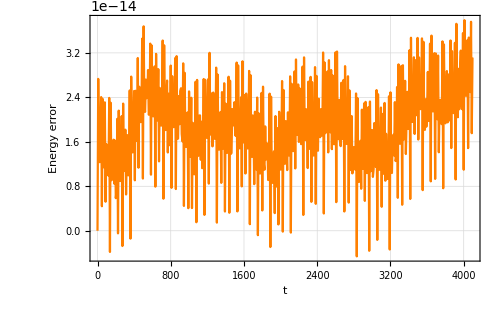

```mathematica
plot=ListPlot[{MeanHamAdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{Orange},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy error"},
LabelStyle->Directive[Black,Bold]
]
```

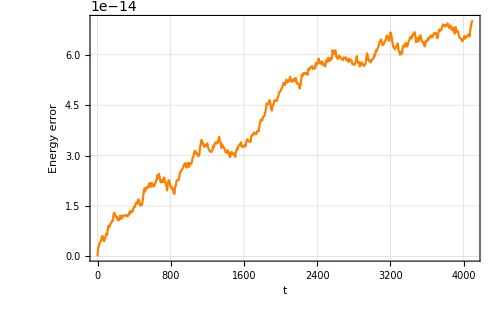

```mathematica
plot=ListPlot[{DesvHamAdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{Orange},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy error"},
LabelStyle->Directive[Black,Bold]
]
```